Corso di Laboratorio Computazionale, Corso di Laurea in Matematica,  Università di Padova.        
A.A. 2021-2022

# Esercizi 4: Julia e Mandelbrot sets

Notebook del gruppo: Pinguini tattici nucleari

Componenti del gruppo: Nicole Mietto e Lorena Escribano Huesca

Se ci sono state collaborazioni e/o aiuti al di fuori del gruppo, dichiararli:
In collaborazione con: 
Aiutato da:

Consegna entro:  10/5/22

```mathematica
SetOptions[EvaluationNotebook[],Background->LightCyan]
```

## Esercizio 4.1: Autosimilarità (approssimata) degli insiemi di Julia e/o di Mandelbrot

## Testo dell’esercizio

### Testo dell’esercizio

Investigare la auto-similarità (approssimata) degli insiemi di Julia e/o dell’insieme di Mandelbrot.  
Creare una successione di ingradimenti successivi di uno (o due, o tre, ma non di più: è meglio la qualità della quantità) Julia sets e/o dell’insieme di Mandlebrot, a  scelta, che ne mostrino nel modo più chiaro possibile, secondo i vostri gusti, l'approssimata autosimilarità.

#### Suggerimenti ed osservazioni:

Usare la finestrella e mostrare il risultato o in una graphics grid oppure in un'animazione.

Cercate di curare il risultato, creando delle immagini che diano un'idea quanto più immediata e convincente possibile dell'autosimilarià. 

Se lo desiderate potete usare una colorazione di vostra scelta.

Saranno ovviamente apprezzati disegni che utilizzino effetti cromatici particolarmente belli, anche se questo non è essenziale per evidenziare la autosimilarità.

NB: Regola generale: Meglio poche immagini chiare e curate che tante disorganizzate.

Nota:
Prima della consegna cancellate gli output dal notebook.
Le immagini verranno ricreate al momento della correzione.
Nel caso la creazione delle immagini richieda tempi lunghi (superiore a una decina di minuti) scrivetelo nel notebook e contattatemi.

## Soluzione

Innanzitutto creamo le funzioni per insiemi di Julia.
Abbiamo incluso il raggio Rc nella funzione j per velocizzarla perché di questa forma non è necessario ricalcolare Rc ad ogni iterazione, utilizzando anche la pure function w^2 + c.
Per poter fare questo usiamo il comando Module, che ci permette di trattare queste variabili come locali (e di consequenza non dobbiamo ricalcolarle ad ogni iterazione) e di fare queste operazioni:
Ad ogni iterazione definiamo un nuovo numero complesso, chiamamolo znew, della seguente forma znew = zold.b2 + c finché non esce dalla palla attorno al origine di raggio r  o non si supera il numero massimo di itarazioni ( i punti che rimangono nel cerchio per un tempo infinito, sono quelli che appartengono all’insieme di Julia)
Il colore del pixel sarà il numero  0.7 (k+1)/(1+nit) (Dove k è il numero di iterazioni che si hanno fatto prima che il punto esca dal cerchio) secondo la tavola implementata in Mathematica Hue, che rapresenta un colore nello spazio di colore HSB con hue 0.7 (k+1)/(1+nit)

Inoltre compilamo la funzione numerica j con il comando f = Compile[ {variabili} ,  espressione ] , dove le variabili si definiscano indicando il tipo di numero:  { {z,_Complex},{nit,_Integer},{c,_Complex}}. 
Compile ci permette anche di velocitare la funzione j perché le istruzioni di funzioni compilate possono essere eseguite da una macchina virtuale che è inclusa nel linguaggio Wolfram. Questa è basata su una macchina a registri idealizzata che utilizza posizioni temporanee (registri) per memorizzare i risultati intermedi mentre vengono calcolati.

Per quanto riguarda la funzione jgrid, usiamo il comando ParallelTable, che lavora come una Table ma in parallelo, e quindi siamo riusciti a velocizzare il processo.
Pertanto, dato un rettangolo (dato come una lista dei suoi vertici: {xmin,xmax},{ymin,ymax} ) facciamo un meshing (cioè dividiamo il rettangolo in rettangoli più piccoli, la cui dimensione dipende dal numero di divisioni) e applichiamo la funzione j a ogni punto creato all’interno del rettangolo.

Alla fine per creare la funzione jset abbiamo usato i seguenti comandi:
Graphics che ci permette disegnare una figura 2-dimensionale
Raster che representa un array di celle di colore
E infine, ColorFunction, Frame e ImageSize che sono funzioni per migliorare la visibilità dell’immagine.

```mathematica
j= Compile[{ {z,_Complex},{nit,_Integer},{c,_Complex}},
             Module[{k=0,w=z,  r=.5+√(.25+Abs[c])},
                                       While[Abs[w]<r  &&   k<nit, w = w^2 + c ; k++];  
                                       0.7 (k+1)/(1+nit) ]
                                 ] ;
jgrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_,c_]:=
                ParallelTable[  j[x+I y,nit,c] ,  {y,ymin,ymax,(ymax-ymin)/ndiv},    {x,xmin,xmax,(xmax-xmin)/ndiv}  ];

jset[{xmin_,xmax_,ymin_,ymax_},ndiv_,numit_,c_, size_]:=
    Graphics[ Raster[  jgrid [{xmin,xmax,ymin,ymax},ndiv,numit,c] ,  {{xmin,ymin},{xmax,ymax}},  ColorFunction->Hue],Frame->True,ImageSize->{ size}
                       ];
```

Facciamo una prova passando come numero complesso alla funzione jset, c = 0.365-0.37 ⅈ
Inoltre fissiamo la dimensione dell’ immagine mettendo 300 come ImageSize.

```mathematica
c=0.365-0.37 I;
```

```mathematica
jset[{-1.5,1.5,-1.2,1.2},400,200,c,300]
```

In seguito implementiamo la funzione finestrella per poter fare uno zoom nelle imagini che genereremo.
Si usano i funzioni: Show per mostrare le line della finestra sul grafico gr ; Graphics usa il comando Line per disegnare un rettangolo dati i suoi vertici.

```mathematica
finestra[gr_,{x1_,x2_,y1_,y2_}]:=
Show[gr,
              Graphics@Line[{{x1,y1},{x2,y1},{x2,y2},{x1,y2},{x1,y1}}]
 ]
```

Proviamola

```mathematica
jp1=jset[{-1.5,1.5,-1.2,1.2},400,200,c,300];
jp1f=finestra[jp1,{-.35,.095,.3,.7}];
jp2=jset[{-.35,.095,.3,.7},400,200,c,300];
```

```mathematica
GraphicsRow[{jp1f,jp2}]
```

Costruiamo ora una successione di immagini  che evidenziano la (quasi) autosimilarità degli insiemi di Julia.

Esempio 1: The Siegel disk fractal 
Lavoramo con la seguente figura: “Siegel disk fractal”, in questo caso passiamo come parametro c= -0.391-0.587ⅈ

```mathematica
Clear[c]
c=-0.391-0.587I;
jset[{-1.5,1.5,-1.2,1.2},400,100,c,300]
```

In seguito definiamo la funzione test che ci permette di fissare il numero di iterazioni (100 iterazioni) , il numero complesso c e la dimensione dell’ immagine (300).

```mathematica
test[dominio_,ndiv_]:=jset[dominio,ndiv,100,c,300]
```

Più  divisioni vi sono, più dettagliato sarà l’insieme Julia quando si esegue uno zoom profondamente, ma sono necessari più calcoli. Più alta è la precisione dei numeri, più a lungo si può zoomare senza incontrare pixel più grandi.

Sovrapponendo la finestra alle immagini ingrandite possiamo osservare chiaramente la autosimilarità degli insiemi di Julia.

```mathematica
ts1=test[{-1.5,1.5,-1.2,1.2},400];
tsf1=finestra[ts1,{-.9,-.4,-.1,.4}];
ts2=test[{-.9,-.4,-.1,.4},300];
tsf2=finestra[ts2,{-.725,-.65,.095,.18}];
ts3=test[{-.725,-.65,.095,.18},300];
tsf3=finestra[ts3,{-.725,-.705,.139,.16}];
ts4=test[{-.725,-.705,.139,.16},500];
tsf4=finestra[ts4,{-.723,-.72,.155 ,.159}];
ts5=test[{-.723,-.72,.155 ,.159},600];
```

```mathematica
GraphicsGrid[{{tsf1,tsf2,tsf3},{tsf4,ts5}},ImageSize->600]
```

Esempio 2: Douady’s rabbit fractal
Adesso lavoramo con la seguente figura: “Douady’s rabbit fractal”, scriviamo  c=-0.123+0.745ⅈ

```mathematica
Clear[c]
c=-0.123+0.745I;
jset[{-1.5,1.5,-1.2,1.2},400,200,c, 300]
```

Proviamo l’ autosimilarità della figura, della stessa forma dell’ esempio precedente.

```mathematica
j1=test[{-1.5,1.5,-1.2,1.2},400];
jf1=finestra[j1,{-1.05,-.85,.68,.95}];
j2=test[{-1.05,-.85,.68,.95},300];
jf2=finestra[j2,{-1.03,-.95,.85,.92}];
j3=test[{-1.03,-.95,.85,.92},300];
jf3=finestra[j3,{-1, -.987,.89,.91}];
j4=test[{-1, -.987,.89,.91},500];
jf4=finestra[j4,{-.996,-.992,.904 ,.909}];
j5=test[{-.996,-.992,.904,.909},600];
```

```mathematica
GraphicsGrid[{{jf1,jf2,jf3},{jf4,j5}},ImageSize->600]
```

Esempio 3:  Insieme di Mandelbrot
L’insieme di Mandelbrot è l’insieme di tutti i punti complessi c che generano un insieme di julia connesso. Siccome un insieme è connesso se e solo se contiene l’origine, per ogni  c  complesso, basta vedere se l’orbita dell’origine scappa all’infinito oppure no. 
Definiamo le funzioni per il MandelBrot come a lezione:
Di nuovo usamo la funzione j, ma questa volta il punto di partenza è l’origine z=0, e si campiona su  c ∈ ℂ , ovvero sulle parti reali ed immaginarie di c, pertanto passiamo come parametro cx+I cy .
La funzione mgrid, proprio come la funzione jgrid, chiama la funzione j e passa come parametri quelli che abbiamo appena discusso. mgrid divide il rettangolo dato in ndiv x ndiv rettangoli più piccoli, e passa come parametro alla funzione j i vertici di questi rettangoli.

Finalmente la funzione mset è l’ equivalente alla funzione jset, e ci permette di disegnare l’insieme di Mandelbrot.
La differenza fra questi due funzioni è che mset non ha bisogno del parametro c, perchè da c, si costruisce una successione per ricorsione:
z_0=0		(termine iniziale)
z_(n+1)=(z^2)_n + c	(successione ricorsiva)

```mathematica
mgrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_]:=
ParallelTable[j[0,nit, cx+ I cy] ,    {cy,ymin,ymax,(ymax-ymin)/ndiv},  {cx,xmin,xmax,(xmax-xmin)/ndiv}  ]
```

```mathematica
mset[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_,imsize_]:=
Show[      Graphics@Raster [
                                mgrid[{xmin,xmax,ymin,ymax},ndiv,nit],
                                {{xmin,ymin},{xmax,ymax}},
                                 ColorFunction->Hue
                                  ],
            Frame->True,
            ImageSize->{imsize}]
```

Disegnamo l’ insieme di Mandelbrot usando la funzione appena definita mset

```mathematica
mset[{-2.,2.,-2.,2.},600,200,400]
```

Proviamo l’ autosimilarità.
Definiamo la funzione prova che ci permette di fissare il numero di iterazioni (100 iterazioni) e la dimensione dell’ immagine (300).

```mathematica
prova[dominio_,ndiv_]:=mset[dominio,ndiv,100,300]
```

```mathematica
m1=prova[{-2.,1.,-1.,1.},400];
mf1=finestra[m1,{-1.7,-1.87,-.05,.05}];
m2=prova[{-1.7,-1.87,-.05,.05},300];
mf2=finestra[m2,{-1.865,-1.86,-.0015,.0015}];
m3=prova[{-1.865,-1.86,-.0015,.0015},300];
```

```mathematica
GraphicsGrid[{{mf1,mf2,m3}},ImageSize->700]
```

## Esercizio 4.2: Insieme di Mandelbrot e dinamica della mappa quadratica

## Testo dell’esercizio

### Testo dell’esercizio

Investigare la relazione fra la struttura dell’insieme di Mandelbrot e le orbite periodiche attrattive del sistema dinamico discreto dato dalle iterazioni del polinomio  P_c(z) = z^2+c.

1. Produrre, per qualche n=1,2,3,.. (arrivare a quel che si desidera, o si riesce), un immagine o un’animazione che, per un opportuno valore di c (dipendente da n),  evidenzi l’esistenza di un’orbita periodica attrattiva di P_c di periodo n all’interno di K_c. Evidenziare, nel Mandelbrot, i valori usati di c. 

2. Posizionare un locator nel Mandelbort che legge c e produce affianco un disegno di K_c con, al suo interno, l’orbita periodica attrattiva.

#### Suggerimenti ed osservazioni:

Per disegnare i punti di un’orbita periodica attrattiva si può per esempio determinare un po’ di punti di una qualunque orbita (nel suo bacino di attrazione) e tenerne solo la `coda’.

1. Se si inseriscono i diversi valori di c in un unico Mandelbrot, indentificarli in modo opportuno (labels, frecce, ..)

2. Per disegnare K_c usare la dinamica (insiemistica) all’indietro, come fatto a lezione.
Per un esempio di uso del locator vedere il notebook della lezione

## Soluzione

In questo esercizio investigheremo la relazione tra le orbite attrattive di periodo n e le regioni dell’insieme di Mendelbrot.

Richiamiamo qui sotto le funzioni ( più efficienti ) già note per Julia e Mendelbrot :

```mathematica
j= Compile[{ {z,_Complex},{nit,_Integer},{c,_Complex}},  Module[{k=0,w=z,  r=.5+√(.25+Abs[c])},  While[Abs[w]<r  &&   k<nit, w = w^2 + c ; k++];  
                                       0.7 (k+1)/(1+nit) ]  ] ;jgrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_,c_]:=   ParallelTable[ j[x+I y,nit,c] , {y,ymin,ymax,(ymax-ymin)/ndiv}, {x,xmin,xmax,(xmax-xmin)/ndiv}];
jset[{xmin_,xmax_,ymin_,ymax_},ndiv_,numit_,c_]:=      Graphics@ Raster[      jgrid [{xmin,xmax,ymin,ymax},ndiv,numit,c] ,     {{xmin,ymin},{xmax,ymax}},ColorFunction->Hue  ];
jset[limiti_,ndiv_,numit_,c_,ImSize_]:= Show[ jset[limiti,ndiv,numit,c],Frame->True,   ImageSize->{ ImSize } ] ;
finestra[gr_,{x1_,x2_,y1_,y2_}]:= Show[   gr,   Graphics@Line[{{x1,y1},{x2,y1},{x2,y2},{x1,y2},{x1,y1}}]   ];
```

```mathematica
mgrid[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_]:=  ParallelTable[j[0,nit, cx+I cy],   {cy,ymin,ymax,(ymax-ymin)/ndiv},  {cx,xmin,xmax,(xmax-xmin)/ndiv}  ];
mset[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_,imsize_]:=
Show[      Graphics@Raster [   mgrid[{xmin,xmax,ymin,ymax},ndiv,nit], {{xmin,ymin},{xmax,ymax}}, ColorFunction->Hue ],
                Frame->True,ImageSize->{imsize}];
```

Sia f: ℂ→ ℂ ( oppure f: ℝ^d→ℝ^d con d≥1 ) funzione definente l’orbita. Con orbita di periodo n si intende un orbita costituita da un insieme di n punti : {  x_0, f[x_0], ...., f^(n-1)[x_0] } continuamente ripercorsi nell’ordine illustrato ( di solito quando si indica periodo n si intende il periodo minimo ).
Un’orbita attrattiva di periodo n è invece un’orbita che in un tempo infinito tende con periodo n a ciascuno dei punti dell’orbita descritta sopra

Per studiare le orbite attrattive di periodo n sarà utile definire una funzione P[ n, c, z ] che applica n volte ad un punto iniziale z la funzione #^2+ c .

```mathematica
P[n_,c_,z_]:=Nest[(#^2+c)&,z,n]
```

caso n=1

Innanzitutto studiamo il caso n = 1. 
Troviamo i punti fissi ( se  f[x_0]= x_0 ⇒ f^t[x_0]=x_0 ∀ t ) .

```mathematica
pf1= z/.Solve[P[1,c,z]== z,z]
```

Calcoliamo ora la derivata in tali punti. 
Sappiamo dalla teoria che se |f’[x]| < 1 tali punti sono attrattivi.

```mathematica
dpf1= D[P[1,c,z],z]/.{z->pf1}
```

Facciamo quindi il grafico sulla regione con -2≤ y (e rispettivamente x ) ≤ 2 in cui sappiamo essere contenuto l’insieme di Mendelbrot.
Intersechiamo inoltre il grafico con il piano di altezza 1 così da poter evidenziare l’insieme dei c che individua orbite attrattive di periodo 1, si tratterà della parte di superficie che si trova al di sotto del piano in azzurro.

```mathematica
g1=GraphicsRow[Table[Plot3D[{Abs[dpf1[[t]]]/.{c->cx+ I cy},1}, {cx,-2,2},{cy,-2,2}],{t,1,2}]]
```

Rappresentiamo ora la frontiera dell’insieme con un ContourPlot nel livello 1

```mathematica
cont1= {ContourPlot[Abs[1-√(1-4 (cx+I cy))]==1,{cx,-2,2},{cy,-2,2},ContourStyle->{Black,Thickness[0.006]}],ContourPlot[Abs[1+√(1-4 (cx+I cy))]==1,{cx,-2,2},{cy,-2,2},ContourStyle->{Black,Thickness[0.006]}]}
```

Notiamo che nella cardioide (“corpo centrale del Mendelbrot”, insieme a sinistra) si trovano le orbite periodiche attrattive di periodo 1. Mentre l’insieme di destra non individua nessuna zona.
Sovrapponiamo quindi la cardioide all’insieme di Mandelbrot.
Mostriamo anche il comportamento asintotico di un’orbita con c che si trova all’interno della cardioide.
Mostriamo ad esempio per c = -0.5 + 0.1 i .

```mathematica
mand=mset[{-2.,1,-1.5,1.5},500,700,500];
```

```mathematica
Show[mand,cont1,Graphics[{Black,Point[{-.5,0.1}]}],Graphics[Style[Text["-0.5 + 0.1 i",{-.5,0.16}],Black, Bold,Small,Background->White]]]
```

Per disegnare l’orbita definiamo delle funzioni che ci saranno utili anche nei casi seguenti:
- orb[ c, z, nit ] : crea la lista di punti del piano complesso ( ℝ×ℝ ) che rappresentano l’orbita del punto z iniziale fino ad nit volte ( utilizzando un NestList che tiene traccia delle iterazioni prima di giungere al risultato finale ).
- orb[ c, z, nit, ncoda] : che mi restituisce gli ultimi ncoda punti ( utile per studiare il comportamento asintotico di un’orbita )
- gorb[ c, z, nit, ncoda] : che rappresenta in un grafico orb[ c, z, nit, ncoda]

```mathematica
orb[c_,z_,nit_]:=Map[  {Re[#],Im[#]}& ,   NestList[ #^2+c &,z,nit]  ]
orb[c_,z_,nit_,ncoda_]:= Take[orb[c,z,nit],-ncoda]
gorb[c_,z_,n_,ncoda_]:=ListPlot[orb[c,z,n,ncoda],PlotRange->2{{-1,1},{-1,1}},PlotStyle->{White,PointSize[0.007]}]
```

Eseguiamo ora un Manipulate per creare un’animazione dell’evoluzione dell’orbita, come punto iniziale scegliamo l’origine ( che sappiamo essere contenuta in in ciascun Julia corrispondente ad un c ∈ Mandelbrot ).
Sovrapponiamola anche all’insieme di Julia corrispondente.

```mathematica
js1=jset[{-2,2,-2,2},300,50,-.5+0.1I,300];
```

```mathematica
Manipulate[Show[js1,   gorb[-.5+.1 I,0,n,5],PlotRange->{{-2,2},{-2,2}},ImageSize->Large] , {n,4,18,1}]
```

Notiamo che verso la quindicesima iterazione i punti quasi si sovrappongono

caso n=2

Per trovare i “punti fissi” delle orbite di periodo 2 itero 2 volte la funzione iniziale : (#^2+ c)^2 + c .

```mathematica
pf2= z/.Solve[ P[2,c,z]==z,z]
```

Togliamo dalla lista di punti quelli contenuti in pf1 ( sicuramente ci saranno poichè un punto fisso di una funzione applicata 1 volta sarà un punto fisso anche di una funzione applicata 2 volte ).

```mathematica
pf2=Complement[pf2,pf1]
```

I due punti rimasti appartengono ad un’unica orbita poichè hanno periodo 2.
Verifichiamo ora se tali punti sono attrattivi calcolando la derivata.

```mathematica
dpf2=D[ P[2,c,z] , z]/.{z->pf2}//Simplify
```

Plottiamone il grafico.
Notiamo che individua il disco a sinistra della cardioide nel Mandelbrot.
Scegliamo c= -1 + 0.1 i per mostrare un esempio di orbita di periodo 2.

```mathematica
g2=Plot3D[{Abs[dpf2[[1]]]/.{c->cx+ I cy},1}, {cx,-2,2},{cy,-2,2}]
```

```mathematica
Show[mand,ContourPlot[Abs[4+4  (cx+ I cy)]==1 ,{cx,-2,2},{cy,-2,2},ContourStyle->{White,Thickness[0.006]}],Graphics[{Black,Point[{-1.1,0.1}]}],Graphics[Style[Text["-1.1 + 0.1 i",{-1.1,0.16}],Black, Bold,Small,Background->White]]]
```

```mathematica
js2=jset[{-2,2,-2,2},300,50,-1.1+0.1I,300];
```

```mathematica
Manipulate[Show[js2,   gorb[-1.1+.1 I,0,n,5],PlotRange->{{-2,2},{-2,2}},ImageSize->Large] , {n,4,18,1}]
```

caso n=3

Procediamo come in precedenza, perciò ricaviamo i punti fissi di un’orbita iterata 3 volte e togliamo dall’insieme i punti fissi di periodo 1.
Calcoliamo poi la derivata.

```mathematica
pf3= z/.Solve[ P[3,c,z]==z,z];
```

```mathematica
pf3= Complement[pf3,pf1];
dpf3= D[P[3,c,z],z]/.{z->pf3};
```

Plottiamone i grafici. Poichè il tempo di esecuzione della cella non è così breve abbiamo reso l’output una cella non eseguibile.

```mathematica
(*g3=GraphicsGrid[Table[Plot3D[{Abs[dpf3[[t+m]]]/.{c->cx+ I cy},1}, {cx,-2,2},{cy,-2,2}],{m,0,3,3},{t,1,3}],ImageSize->Large]*)
```

```mathematica
cont3=Table[ContourPlot[ Abs[ dpf3[[t]]/. c->cx+I cy]==1  , {cx,-2.,2.},{cy,-2.,2},ContourStyle->{Magenta}],{t,1,6}]
```

Notiamo che i ContourPlot che individuano un insieme attrattivo sono quelli che si trovano nella posizione 2,3,4 e 5 dell’insieme.
Vorremmo che gli insiemi fossero a 3 a 3 uguali.... in questo modo se mi trovo all’interno dell’insieme comune vengo attratto con periodo 3 da ognuno dei punti fissi di periodo 3 che individuano tale insieme.
Sovrapponiamo ora le zone individuate e notiamo che potrebbe trattarsi di un problema di ordinamento delle radici (poichè gli insiemi nelle posizioni 4 e 5 quasi si completano ). Sappiamo che in Mathematica vengono ordinate in ordine crescente per la propria parte reale.

```mathematica
Show[cont3[[2]],cont3[[3]],cont3[[4]],cont3[[5]],ImageSize->Large]
```

Come già fatto a lezione aiutiamo la visualizzazione dello scambio di ordinamento delle radici con l’uso di un locator dinamico.
Ridefiniamo i ContourPlot che ci interessano con un maggior numero di PlotPoints in modo tale da ottenere una figura più precisa.

```mathematica
cont32=Table[ContourPlot[ Abs[ dpf3[[t]]/. c->cx+I cy]==1  , {cx,-2.,2.},{cy,-2.,2},ContourStyle->Magenta,PlotPoints->30],{t,4,5}];
```

Chiamiamo zigzag la figura su cui vogliamo poi posizionare un locator. Scegliamo il disco situato più in basso.

```mathematica
zigzag=Show[  cont32[[1]],cont32[[2]]  ,PlotRange-> {{-.25,0.},{-.9,-.6}},ImageSize->Large];
```

Definiamo poi la funzione che mi ritorna la parte reale e immaginaria degli zeri.

```mathematica
Zeri[cc_]:=Map[{Re[#],Im[#]}&,  pf3/.c->cc   ]
```

Qui sotto riportiamo una funzione che rappresenta nel piano gli zeri trovati sopra, differenziandoli contrassegnando ognuno di essi con un’etichetta numerica.

```mathematica
PlZeri[{cx_,cy_}]:=Show[  Graphics[   Table[ Style[Text[j,Zeri[cx+I cy][[j]]],Red,Bold,Medium],{j,6}]    ] , PlotRange->{{-2,2},{-2,2}}, Axes->True, Ticks->None,ImageSize->Large]
```

Infine mostriamo grazie ad un DynamicModule con locator la distribuzione degli zeri nel piano data la posizione nell’insieme.

```mathematica
DynamicModule[{cc={-0.1,0.7}},{LocatorPane[Dynamic[cc],zigzag],Dynamic@PlZeri[cc]}]
```

Notiamo, come già anticipato, che nella “spaccatura” del disco gli zeri nella posizione 4 e 5 si scambiano.
Mostriamo ora un esempio di orbita 3-periodica scegliendo c= - 0.1 - 0.75 i  con punto iniziale 0.

```mathematica
Show[mand,ContourPlot[ Abs[ dpf3[[2]]/. c->cx+I cy]==1  , {cx,-2.,2.},{cy,-2.,2},ContourStyle->{Yellow,Thickness[0.006]}],Graphics[{Black,Point[{-.1,-.75}]}],Graphics[Style[Text["-0.1 - 0.75 i",{-0.1,-0.82}],Black, Bold,Small,Background->White]]]
```

```mathematica
js3=jset[{-2,2,-2,2},300,50,-0.1-0.75I,300];
```

```mathematica
Manipulate[Show[js3,   gorb[-0.1-0.75I,0,n,9],PlotRange->{{-2,2},{-2,2}},ImageSize->Large] , {n,8,18,1}]
```

caso n=4

Togliamo dall’insieme dei punti fissi quelli di periodo 1 e 2 ( sono punti fissi anche della funzione iterata 4 volte )

```mathematica
pf4= z/.Solve[ P[4,c,z]==z,z];
```

```mathematica
pf4= Complement[pf4,pf1,pf2];
dpf4= D[P[4,c,z],z]/.{z->pf4};
```

Plottiamone i grafici. Poichè il tempo di esecuzione della cella non è così breve abbiamo reso l’output una cella non eseguibile.

```mathematica
(*cont4=Table[ContourPlot[ Abs[dpf4[[t]]/.c-> cx + I cy ]== 1, {cx,-2.,2.},{cy,-2.,2},ContourStyle->{Black}],{t,1,12}]*)
```

Notiamo che gli insiemi non sembrano completarsi con molta precisione. 
Qui sotto aumentiamo i PlotPoints a 100, notiamo che si aggiunge un nuovo insieme che prima non era stato nemmeno individuato.
Poichè la velocità di esecuzione non è così elevata abbiamo deciso di rendere le celle non eseguibili ( tempo di esecuzione di oltre 6 minuti ).
Per poi mostrare che le quattro immagini si suddividono in più di quattro grafici per motivi di ordinamento delle radici, utilizziamo un DynamicModule.

```mathematica
cont[f_]:= ContourPlot[ Abs[f/.c-> cx + I cy ]== 1, {cx,-2.,2.},{cy,-2.,2},ContourStyle->{Black},PlotPoints->100]
```

```mathematica
(*cg4=Map[cont[dpf4[[#]]]&,Range[12]]*)
```

Dai grafici prodotti si può notare che zone diverse di uno stesso grafico si completano in grafici seguenti. In totale si formano con oppportune combinazioni 4 grafici uguali.
Il disco più a sinistra del 3°, 4°, 8° grafico sembra completo, mentre unendo pezzi di grafico sulla sinistra del 5°, 6° e 7° otteniamo un disco simile agli altri.

```mathematica
(*zigzag567sx=Show[ cg4[[5]]  ,cg4[[6]],cg4[[7]],PlotRange-> {{-1.4,-1.23},{-.1,.1}},ImageSize->Medium,PlotLabel->Style[" 5°, 6° e 7°",20,Black]]*)
```

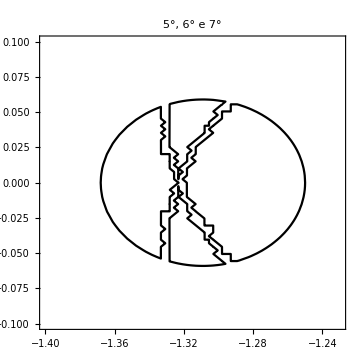
```mathematica
discosx=-Graphics-;
```

I due dischi simmetrici ( essendo simmetrici anaizziamo solo il disco inferiore ) rispetto all’asse x più a destra sono completi solo nella 9° figura, mentre per ottenere i rimanenti:
- uniamo il 3° e 4°;
- uniamo il 5° e il 6°;
- uniamo il 7° e l’8°.

```mathematica
(*zigzag34dx=Show[  cg4[[3]],cg4[[4]],PlotRange-> {{.23,0.33},{-.48,-.58}},ImageSize->Medium,PlotLabel->Style[" 3° e 4°",20,Black]]*)
```

```mathematica
(*zigzag56dx=Show[  cg4[[5]],cg4[[6]],PlotRange-> {{.23,0.33},{-.48,-.58}},ImageSize->Medium,PlotLabel->Style[" 5° e 6°",20,Black]]*)
```

```mathematica
(*zigzag78dx=Show[  cg4[[7]],cg4[[8]],PlotRange-> {{.23,0.33},{-.48,-.58}},ImageSize->Medium,PlotLabel->Style[" 7° e 8°",20,Black]]*)
```

Per gli altri dischi più piccoli notiamo che sono sempre ben definiti ma in grafici differenti

Ridefiniamo la funzione Zeri4 e PlZeri4 per la funzione applicata 4 volte

```mathematica
Zeri4[cc_]:=Map[{Re[#],Im[#]}&,  pf4/.c->cc   ]
```

```mathematica
PlZeri4[{cx_,cy_}]:=Show[  Graphics[   Table[ Style[Text[j,Zeri4[cx+I cy][[j]]],Red,Bold,Medium],{j,12}]    ] , PlotRange->{{-2,2},{-2,2}}, Axes->True, Ticks->None,ImageSize->Medium]
```

Poichè il procedimento è sempre lo stesso mostriamo solo per il disco più a sinistra lo scambio di posizione degli zeri.
Vediamo che al passaggio tra il 5° e il 6° grafico si scambiano il 5° e il 6° zero e tra il 6° e 7° grafico il 6° e 7° zero.

```mathematica
DynamicModule[{cc={-1.35,0}},{LocatorPane[Dynamic[cc],discosx],Dynamic@PlZeri4[cc]}]
```

Mostriamo le zone corrispondenti alle orbite 4 periodiche e scegliamo c=0.30 - 0.54 i che si trova nel disco di destra più in basso.
Mostriamo poi un ingrandimento delle zone più piccole per avere un’idea più chiara dell’insieme.

```mathematica
(*Show[mset[{-.2,-.1,-1.1,-1.},500,700,500],cg4[[10]],ImageSize->Large,PlotRange->{{-0.2,-0.1},{-1.1,-1.}}]*)
```

```mathematica
(*Show[mand,cg4[[8]],cg4[[9]],cg4[[10]],Graphics[{Black,Point[{0.3,-.54}]}],Graphics[Style[Text["0.3 - 0.54 i",{0.3,-0.62}],Black, Bold,Small,Background->White]],ImageSize->Large]*)
```

```mathematica
js4=jset[{-2,2,-2,2},300,50,0.3-0.54I,300];
```

```mathematica
Manipulate[Show[js4,   gorb[0.3-0.54I,0,n,12],PlotRange->{{-2,2},{-2,2}},ImageSize->Large] , {n,11,18,1}]
```

caso n=5

Togliamo dall’insieme dei punti fissi quelli di periodo 1 ( sono punti fissi anche della funzione iterata 5 volte )

```mathematica
pf5= z/.Solve[ P[5,c,z]==z,z];
```

```mathematica
pf5= Complement[pf5,pf1];
dpf5= D[P[5,c,z],z]/.{z->pf5};
```

Plottiamone i ContourPlot.

```mathematica
(*cont52=Table[ContourPlot[ Abs[dpf5[[t]]/.c-> cx + I cy ]== 1, {cx,-2.,2.},{cy,-2.,2},ContourStyle->{Black}],{t,1,30}]*)
```

I tempi di esecuzione sono davvero lunghi quindi abbiamo riportato l’output come immagine. Utilizzando comunque numero di PlotPoints minore si possono ottenere tutti grafici vuoti.
Notiamo che i grafici non vuoti si possono facilmente combinare in 5 immagini simili. Mostriamo qui sotto le zone in cui ci aspettiamo di trovare un’orbita 5-periodica attrattiva.
Scegliamo c = -0.5 - 0.55 i per rappresentarne un esempio.

```mathematica
(*Show[mand,cont52[[10]],cont52[[17]],Graphics[{Black,Point[{-.5,-0.55}]}],Graphics[Style[Text["-0.5 - 0.55 i",{-0.5,-0.48}],Black, Bold,Small,Background->White]],ImageSize->Large]*)
```

```mathematica
js5=jset[{-2,2,-2,2},300,50,-0.5-0.55I,300];
```

```mathematica
Manipulate[Show[js5,   gorb[-0.5-0.55I,0,n,15],PlotRange->{{-2,2},{-2,2}},ImageSize->Large] , {n,14,18,1}]
```

Abbiamo provato anche un altro metodo meno preciso, che ricorda le funzioni usate per disegnare Julia e Mendelbrot.
Ci permette di inviduare una possibile zona attrattiva ( possibile perchè in questo caso abbiamo campionato su una griglia di 10000 elementi )
Innanzitutto definiamo una funzione di base cont5[z] che mi restituisce la parte intera di 1/(|z|) useremo poi il risultato per creare un’entrata della matrice che darà le direttive di colorazione per Raster.
In questo modo creeremo un immagine in bianco e nero, dove vedremo in bianco le possibili zone attrattive. Infatti 1/(|z|)>1 ⇔ |z|<1 lo valuteremo con z valore della derivata in una delle radici.

```mathematica
cont5[z_]:=Floor[1/Abs[z]]
```

Creiamo una funzione divisioni[xmin, xmax, ymin, ymax, ndiv ] che mi crea la Table dei valori di sostituzione su cui lavoreremo. Creiamo poi una Table con 100 divisioni sul quadrato di lato 4 centrato nell’origine.
Abbiamo provato anche un tentativo di calcolo in parallelo utilizzando funzioni più simili a quelle usate per Julia e Mandelbrot ma i tempi di esecuzione previsti erano più lunghi ( più di 3 ore ).
Questo metodo ha comunque un tempo di esecuzione minore ( un po’ meno di un’ora ) ma ha un deficit di grafica e precisione.
Poichè i tempi sono comunque lunghi riportiamo il risultato come immagine.

```mathematica
divisioni[xmin_,xmax_,ymin_,ymax_,ndiv_]:=Table[cx+I cy,{cy,ymin,ymax,(ymax-ymin)/ndiv},{cx,xmin,xmax,(xmax-xmin)/ndiv}]
```

```mathematica
div=divisioni[-2.,2.,-2.,2.,100]
```

Mostriamo che la Table non contiene zeri altrimenti otterremmo una forma indeterminata

```mathematica
Count[div,0,2]
```

0

Definiamo cont5grid[t] che calcola il valore delle derivate nei punti di div e poi gli applica la funzione iniziale.
Otteniamo una lista di profondità due che poi valuteremo con Graphics[Raster[....]] in cont5gr.

```mathematica
cont5grid[t_]:=Map[cont5[dpf5[[t]]/. c->#]&,div,{2}]
```

```mathematica
cont5gr[xmin_,xmax_,ymin_,ymax_,t_]:=Graphics[Raster[cont5grid[t],{{xmin,ymin},{xmax,ymax}}]]
```

```mathematica
(*graf=Table[cont5gr[-2.,2.,-2.,2.,t],{t,1,30}]*)
```

Vediamo che si formano 5 immagini uguali ( unendo la 15° e la 17° ).
Notiamo anche che il c scelto in precedenza si trova all’interno dell’insieme.

```mathematica
(*Show[graf[[8]],Frame->True,ImageSize->Large]*)
```

```mathematica
(*{Show[graf[[15]],ImageSize->Large,Frame->True],Show[graf[[17]],ImageSize->Large,Frame->True]}*)
```

Ora vogliamo costruire una funzione che, con l’uso di un Locator, legge c nel MandelBrot e riproduce l’insieme di Julia corrispondente con un’orbita attrattiva al suo interno. Qui la costruiamo per orbite attrattive di periodo≤8.

Definiamo una funzione di verifica che restituisce un numero che corrisponde al numero di iterazioni≤100 per cui l’orbita rimane dentro al disco di raggio 2.
Questo ci servirà per evitare errori di overflow ( per non calcolare con lo stesso numero di iterazioni le orbite che tendono all’infinito ).

```mathematica
verifica[z_,c_]:=Module[{n=0,z1=z},While[Abs[z1^2+c]<2 && n<100,z1=z1^2+c;n=n+1];n]
```

La funzione period1 mi restituisce il periodo delle orbite attrattive ≤ 8 .
Utilizziamo un Module,con variabile locale periodo a cui assegnamo come valore di defoult 1, per poter eseguire più operazioni.
Al suo interno definiamo l’orbita calcolata su 100 iterazioni, si esegue poi un While finchè la variabile periodo è ≤ 8 in AND con il conteggio dei valori delle distanze tra le ultime 5 iterazioni di f^periodo ≥ 0.005 ( abbiamo scelto un valore arbitrario abbastanza piccolo ), con f intendiamo l’orbita definita sopra, che incrementa di 1 il periodo.
La funzione restituisce, infine, il periodo.

```mathematica
period1[cc_,z_]:=Module[{periodo= 1},orbita=orb[cc,z,100];While[periodo<=8 && Count[Map[Abs[#[[1]]+I#[[2]]]<0.005 &,Table[orbita[[101-t*periodo]]-orbita[[101-(t+1)*periodo]],{t,0,5}]],False]>=1,periodo=1+periodo];periodo]
```

Descr[c] ha il compito di descrivere l’orbita restituendo una lista con una stringa che descrive l’orbita, z iniziale dell’orbita che poi andremo a disegnare e il periodo.
Si tratta di un Module con le seguenti variabili locali:
- z punto iniziale dell’orbita, a cui assegnamo valore di defoult 0 poichè c è contenuto nel Mandelbrot⇔ 0 è contenuto nell’insieme di Julia corrispondente (quindi è un punto che è certamente contenuto nell’insieme di Julia se c in Mand.).
-z2 un valore Random che ha la funzione di assegnare eventualmente il suo valore a z.
- p, il periodo
- nit, n° di iterazioni che se supera una certa soglia ( abbiamo scelto 30 ) non si cercano ulteriori orbite attrattive.
-n che verifica se è ≤100 che 0 si trovoi nell’insieme di Julia.

Si esegue poi il primo If  che calcola p=period1[c,0] se n≥100 altrimenti non fa nulla.
Il secondo If se il periodo calcolato è<9 non fa nulla altrimenti cerca finchè nit<30 altri valori di z per cui si potrebbe trovare un valore p<9.
Si assegna poi str in base ai valori ottenuti.

```mathematica
descr[c_]:=Module[{z=0,z2=RandomReal[{-2,2}]+RandomReal[{-2,2}] I,p=9,nit=1,str="",n=verifica[0,c]},
If[n>=100,p=period1[c,0],None];If[p<9,None,While[  n>=100 && nit<30 && p==9 , While[verifica[z2,c]<100,z2=RandomReal[{-2,2}]+RandomReal[{-2,2}] I];
z=z2;
p=period1[c,z2];nit=nit+1]];str=If[n<100,"c = "<>ToString[c]<>", z = "<>ToString[z]<>", l'orbita scappa all'infinito",If[p<=8,"c="<>ToString[c]<>", z = "<>ToString[z]<>", orbita attrattiva di periodo "<>ToString[p],"c="<>ToString[c]<>", z = "<>ToString[z]<>", orbita non di periodo≤8"]];{str,z,p}]
```

```mathematica
mand=mset[{-2.,1,-1.5,1.5},400,700,450];
```

Eseguiamo poi un DynamicModule similmente a quanto visto per rappresentare gli zeri nel piano.

```mathematica
DynamicModule[{cc={0.,0.}},{LocatorPane[Dynamic[cc],mand],Dynamic@ Manipulate[Module[{d=descr[cc[[1]]+cc[[2]] I]},Show[jset[{-2,2,-2,2},200,150,cc[[1]]+cc[[2]] I], gorb[cc[[1]]+cc[[2]] I,d[[2]],n,9],PlotRange->{{-2,2},{-2,2}},Frame->True,ImageSize->400,PlotLabel->d[[1]]]] ,{n,8,21,1}]}]
```